```mathematica
$Assumptions=A∈Integers&&NN∈Integers
```

A∈Integers&&NN∈Integers

```mathematica
f = A * (1/NN)
```

A/NN

```mathematica
FullSimplify[Sum[Cos[(2Pi)*f*(DT)*n]Exp[-2Pi*I*(f+x)*n],{n,a,b}]]
```

$Aborted

```mathematica
Clear[f]
```

```mathematica
FFT[k_, f_, a_, b_,NN_]:=Sum[Cos[2Pi*f*n] *Exp[-I*2Pi* k * n],{n,a,b}]//FullSimplify
```

```mathematica
FFT[k,f,a,b,NN]
```

$Aborted

```mathematica
Clear[NN]
```

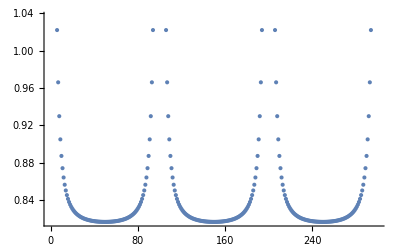

```mathematica
ListPlot[Table[{k, Abs[FFT[k, 1, 0, 100, 100, 0.001]]^2}, {k, 1, 300}]]
```

```mathematica
FFT[1, 0, 0, 10, 100]
```

-(-1)^(4/5) (1+(-1)^(1/50)+(-1)^(1/25)+(-1)^(3/50)+(-1)^(2/25)+(-1)^(1/10)+(-1)^(3/25)+(-1)^(7/50)+(-1)^(4/25)+(-1)^(9/50)+(-1)^(1/5))

```mathematica
NN=1000;
datapoints[f_,a_,b_]:=Table[If[a < n < b,Cos[2Pi*f*n],0],{n,0, NN-1}];
```

```mathematica
FourierTransform[datapoints[f,a,b]]
```

FourierTransform::argmu: FourierTransform called with 1 argument; 3 or more arguments are expected.

General::stop: Further output of FourierTransform::argmu will be suppressed during this calculation.

{FourierTransform[If[a<0<b,Cos[2 π f n],0]],FourierTransform[If[a<1<b,Cos[2 π f n],0]],FourierTransform[If[a<2<b,Cos[2 π f n],0]],FourierTransform[If[a<3<b,Cos[2 π f n],0]],FourierTransform[If[a<4<b,Cos[2 π f n],0]],FourierTransform[If[a<5<b,Cos[2 π f n],0]],FourierTransform[If[a<6<b,Cos[2 π f n],0]],987,FourierTransform[If[a<994<b,Cos[2 π f n],0]],FourierTransform[If[a<995<b,Cos[2 π f n],0]],FourierTransform[If[a<996<b,Cos[2 π f n],0]],FourierTransform[If[a<997<b,Cos[2 π f n],0]],FourierTransform[If[a<998<b,Cos[2 π f n],0]],FourierTransform[If[a<999<b,Cos[2 π f n],0]]}
 |  |  |  |

```mathematica
x[t_]:=If[
```

FourierTransform

```mathematica
Integrate[Cos[2Pi*ω*t]*Exp[-2Pi*I*ξ*t],{t,a,b}]
```

(ⅇ^(-2 ⅈ (a+b) π ξ) (ⅇ^(2 ⅈ b π ξ) (-ⅈ ξ Cos[2 a π ω]+ω Sin[2 a π ω])+ⅈ ⅇ^(2 ⅈ a π ξ) (ξ Cos[2 b π ω]+ⅈ ω Sin[2 b π ω])))/(2 π (ξ-ω) (ξ+ω))

```mathematica
Clear[a,b,NN,f]
```

```mathematica
FullSimplify[Sum[Cos[2Pi*f*n] *Exp[-I*2Pi* k * n/NN],{n,a,b}]]
```

1/(4 (Cos[2 f π]-Cos[(2 k π)/NN]))ⅇ^(-(2 ⅈ (1+a+b) (k+f NN) π)/NN) (ⅇ^((2 ⅈ (k+a k+a f NN) π)/NN)-ⅇ^((2 ⅈ (a k+(1+a) f NN) π)/NN)-ⅇ^((2 ⅈ ((2+b) k+(1+b) f NN) π)/NN)+ⅇ^((2 ⅈ ((1+b) k+(2+b) f NN) π)/NN)+ⅇ^((2 ⅈ ((1+b) k+(2 a+b) f NN) π)/NN)-ⅇ^((2 ⅈ ((2+b) k+(1+2 a+b) f NN) π)/NN)-ⅇ^((2 ⅈ (a k+(1+a+2 b) f NN) π)/NN)+ⅇ^((2 ⅈ ((1+a) k+(2+a+2 b) f NN) π)/NN))

```mathematica
Sum[Cos[2Pi*f*n] *Exp[-I*2Pi* f * n],{n,a,b}]//FullSimplify
```

(1+b-ⅇ^(4 ⅈ f π)-b ⅇ^(4 ⅈ f π)-ⅇ^(-4 ⅈ (-1+a) f π)+ⅇ^(-4 ⅈ b f π)+a (-1+ⅇ^(4 ⅈ f π)))/(2-2 ⅇ^(4 ⅈ f π))

```mathematica
Clear[f,a,b]

F[k_,f_,a_,b_,N_]:=Sum[Cos[2Pi*f*n] *Exp[-I*2Pi* k * n/N],{n,a,b}]
```

(1+b-ⅇ^(4 ⅈ f π)-b ⅇ^(4 ⅈ f π)-ⅇ^(-4 ⅈ (-1+a) f π)+ⅇ^(-4 ⅈ b f π)+a (-1+ⅇ^(4 ⅈ f π)))/(2-2 ⅇ^(4 ⅈ f π))

```mathematica
kVals = Table[F[k,0.05, 0, 1000, 2000],{k,1, 200}];
```

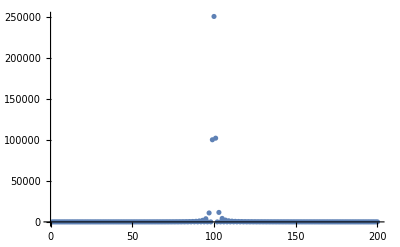

```mathematica
ListPlot[Abs[kVals]^2, PlotRange->All]
```

```mathematica
FullSimplify[Sum[Cos[2Pi*f*n] *Exp[-I*2Pi* f * n],{n,a,b}]]
```

(1+b-ⅇ^(4 ⅈ f π)-b ⅇ^(4 ⅈ f π)-ⅇ^(-4 ⅈ (-1+a) f π)+ⅇ^(-4 ⅈ b f π)+a (-1+ⅇ^(4 ⅈ f π)))/(2-2 ⅇ^(4 ⅈ f π))

```mathematica
Clear[NN]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

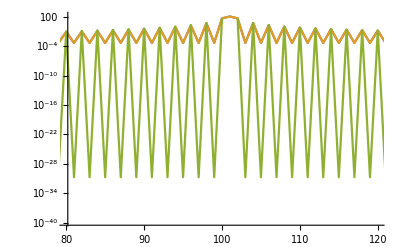

```mathematica
f=0.05;
NN=2000;
a=0;
b=1000;
(*xs = Table[If[a≤n≤b,Cos[2Pi*f*n],0],{n,0,NN-1}];*)
(*ks= Fourier[xs];*)
analyticKs=Table[Sum[Cos[2Pi*f*n] *Exp[-I*2Pi* k * n/NN],{n,a,b}],{k,0,500}];
analyticForm =125*Table[FullSimplify[(Sin[2Pi*(k-100)*0.25]/(2Pi*(k-100)*0.25))^2],{k,0,500}];
(*ListPlot[xs]*)
ListLogPlot[
{
Abs[ks]^2,
0.0005*Abs[analyticKs]^2,
analyticForm
},
PlotRange->{{80,120}, All},Joined->True]
```

```mathematica
res = Table[1/2 ⅇ^(-(2 ⅈ (k+f NN) π)/NN) (1+ⅇ^(4 ⅈ f π)),{k,0,1000}]//N;
```

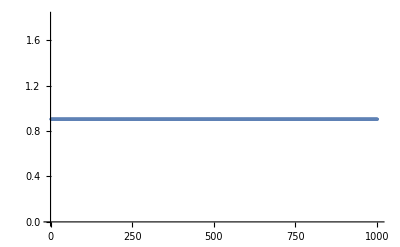

```mathematica
ListPlot[Abs[res]^2,PlotRange->All]
```

```mathematica
Clear[f,NN,a,b]
```

```mathematica
$Assumptions = a∈Integers&&b∈Integers&&x∈Integers&&NN∈Integers&&F∈Integers
```

a∈Integers&&b∈Integers&&x∈Integers&&NN∈Integers&&F∈Integers

```mathematica
FullSimplify[Series[Sum[Cos[2Pi*F*n/NN] *Exp[-I*2Pi* (F+x) * n/NN],{n,a,b}],{x,0,1}]]
```

(1+b-ⅇ^((4 ⅈ F π)/NN)-b ⅇ^((4 ⅈ F π)/NN)-ⅇ^(-(4 ⅈ (-1+a) F π)/NN)+ⅇ^(-(4 ⅈ b F π)/NN)+a (-1+ⅇ^((4 ⅈ F π)/NN)))/(2-2 ⅇ^((4 ⅈ F π)/NN))-1/(2 (-1+ⅇ^((4 ⅈ F π)/NN))^2 NN)ⅈ ⅇ^(-(2 ⅈ (1+2 a+2 b) F π)/NN) (-2 ⅇ^((2 ⅈ (3+2 a) F π)/NN)-2 (-1+a) ⅇ^((2 ⅈ (3+2 b) F π)/NN)+2 a ⅇ^((2 ⅈ (5+2 b) F π)/NN)-(-1+a) a ⅇ^((2 ⅈ (1+2 a+2 b) F π)/NN)+2 (-1+a) a ⅇ^((2 ⅈ (3+2 a+2 b) F π)/NN)-(-1+a) a ⅇ^((2 ⅈ (5+2 a+2 b) F π)/NN)+b^2 ⅇ^((2 ⅈ (1+2 a+2 b) F π)/NN) (-1+ⅇ^((4 ⅈ F π)/NN))^2+b ⅇ^((2 ⅈ (1+2 a) F π)/NN) (-1+ⅇ^((4 ⅈ F π)/NN)) (-2+ⅇ^((4 ⅈ b F π)/NN) (-1+ⅇ^((4 ⅈ F π)/NN)))) π x+O[x]^2

```mathematica
FullSimplify[Series[Eigensystem[{{0, t, 0},{t, 1, t},{0,t,0}}],{t,0,0}]]
```

{{0,O[t]^2,1+O[t]^1},{{-1,0,1},{1,O[t]^1,1},{1,1/t+O[t]^1,1}}}